```mathematica
Quit
```

```mathematica
ky=1;
```

```mathematica
w1=Integrate[√(1- x^2),x];
w2=Integrate[√(1-ky y^2),y];
Simplify[%];
u=FullSimplify[w1+w2]
```

1/2 (x √(1-x^2)+y √(1-y^2)+ArcSin[x]+ArcSin[y])

```mathematica
ux=D[u,x]//Simplify
uy=D[u,y]//Simplify
uyux=uy/ux
```

√(1-x^2)

√(1-y^2)

(√(1-y^2))/(√(1-x^2))

```mathematica
sol=DSolve[{ y'[x]==(√(1-ky y[x]^2))/(√(1-x^2))},y[x],x];
sol=Simplify[sol]
```

{{y[x]→Sin[ArcSin[x]+C[1]]}}

```mathematica
vt=y-(Sin[√ky (ArcSin[x]+c2)]/(√ky));
yt=Sin[√ky (ArcSin[x]+c2)]/(√ky);
```

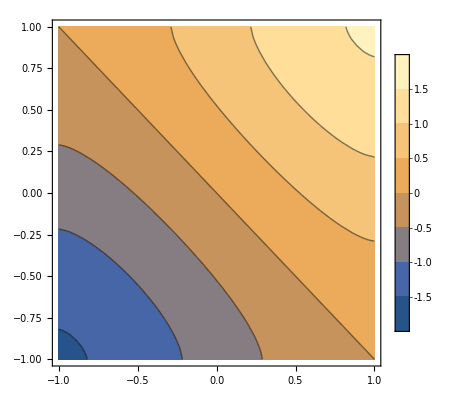

```mathematica
ϵ=0.0001;
ContourPlot[u,{x,-1+ϵ,1-ϵ},{y,(-1+ϵ)/(√ky) ,(1-ϵ)/(√ky)},AspectRatio->1/(√ky),PlotLegends->Automatic]
```

```mathematica
tst=D[vt,x]D[u,x]+D[vt,y]D[u,y];
tst=Simplify[tst];
FullSimplify[tst/.y->yt];
tst=FullSimplify[%]
```

-Cos[c2+ArcSin[x]]+√(Cos[c2+ArcSin[x]]^2)

```mathematica
t1=-Cos[√ky (c2+ArcSin[x])];
t2=√(Cos[√ky (c2+ArcSin[x])]^2);
```

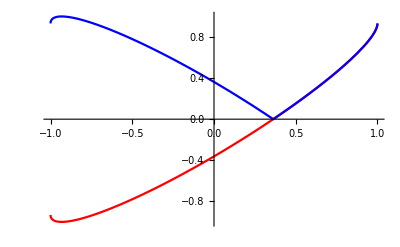

```mathematica
Plot[{t1/.c2->1.2,t2/.c2->1.2},{x,-1,1},PlotStyle->{Red,Blue}]
```

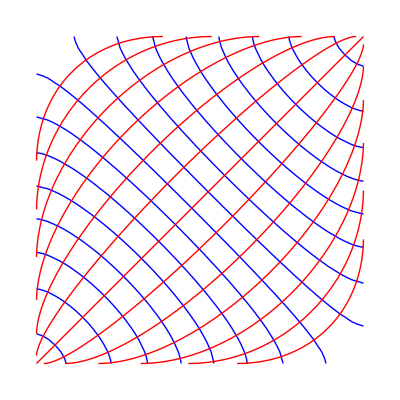

```mathematica
ϵ=0.0001;
g1=ContourPlot[{u==-1.5,u==-1.3,u==-1.1,u==-0.9,u==-0.7,u==-0.5,u==-0.3,u==-0.1,
                             u==0.1,u==0.3,u==0.5,u==0.7,u==0.9,u==1.1,u==1.3,u==1.5},
{x,-1+ϵ,1-ϵ},{y,-1/(√ky)+ϵ,1/(√ky)-ϵ},ContourStyle->{{Thickness[0.0025],Blue}},Axes->None,Frame->None,
ContourShading->False,AspectRatio->1/(√ky)];

yt[x_,c2_]:=Sin[c2+ArcSin[x]]
yplt[x_,c2_]:=If[c2<0,If[x<Sin[c2-π/2],(-2-yt[x,c2]),yt[x,c2]],
                                                      If[x>Sin[c2+π/2],(2-yt[x,c2]),yt[x,c2]]]
g2=Plot[{yplt[x,c2]/.c2->-1.8,yplt[x,c2]/.c2->-1.5,yplt[x,c2]/.c2->-1.2,yplt[x,c2]/.c2->-0.9,yplt[x,c2]/.c2->-0.6,yplt[x,c2]/.c2->-0.3,yplt[x,c2]/.c2->0,yplt[x,c2]/.c2->1.8,yplt[x,c2]/.c2->1.5,yplt[x,c2]/.c2->1.2,yplt[x,c2]/.c2->0.9,yplt[x,c2]/.c2->0.6,yplt[x,c2]/.c2->0.3},
{x,-1+ϵ,1-ϵ},PlotStyle->{{Thickness[0.0025],Red}},AspectRatio->1/(√ky),Axes->None,PlotRange->{{-1,1},{-1,1}}];
Show[g1,g2]
```

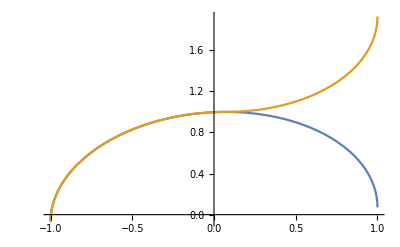

```mathematica
yt[x_,c2_]:=Sin[c2+ArcSin[x]]

yplot[x_,c2_]:=If[c2<0,If[x<Sin[c2-π/2],(-2-yt[x,c2]),yt[x,c2]],If[x>Sin[c2+π/2],(2-yt[x,c2]),yt[x,c2]]]


Plot[{yt[x,c2]/.c2->1.5,yplot[x,c2]/.c2->1.5},{x,-1,1}]
```

```mathematica
yplot[x,c2]/.c2->1.5
```

Sin[1.5+ArcSin[x]]

```mathematica
xt=Sin[1.5-π/2]
```

-0.0707372

```mathematica
yt=.
```